# Notebook for: Numerical study of the gravitational shock wave inside a spherical charged black hole by Eilon & Ori

Geoff Cope
University of Utah
February 3rd, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Paper

```mathematica
Hyperlink["Numerical study of the gravitational shock wave inside a spherical charged black hole",
"paper - Eilon & Ori"]
```

Numerical study of the gravitational shock wave inside a spherical charged black holepaper - Eilon & OriNonepaper - Eilon & Ori

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 7 Kb

{Utilities`CleanSlate`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[μ]-> dμ , 
Dt[η]-> dη , 
Dt[ν]-> dν , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[ϱ]-> dϱ , 
Dt[φ] -> dφ ,
Dt[ξ]-> dξ ,  
Dt[Δ]-> dΔ , 
Dt[δ]-> dδ , 
Dt[ω]-> dω , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓋]-> d𝓋 , 
Dt[𝓊]-> d𝓊 ,
Dt[𝓍]-> d𝓍 ,
Dt[𝓎]-> d𝓎,   
Dt[𝓏] -> d𝓏,
Dt[T]-> dT,
Dt[X]-> dX, 
Dt[Y]-> dY,
Dt[Z]-> dZ,
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ
};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[μ]→dμ
Dt[η]→dη
Dt[ν]→dν
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[ϱ]→dϱ
Dt[φ]→dφ
Dt[ξ]→dξ
Dt[Δ]→dΔ
Dt[δ]→dδ
Dt[ω]→dω
Dt[𝓉]→d𝓉
Dt[𝓋]→d𝓋
Dt[𝓊]→d𝓊
Dt[𝓍]→d𝓍
Dt[𝓎]→d𝓎
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
a/:Dt[a]=0  ;  
b /: Dt[b] = 0 ;  
M /: Dt[M] = 0 ;  (* For Schwarzschild Mass *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

```mathematica
Clear[eq1]
eq1 = 
-  Exp[σ[u,v]] du dv + r[u,v]^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

-du dv ⅇ^σ[u,v]+r[u,v]^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric1]
metric1 = 
lineToMetric[ eq1 , {du,dv,dθ,dϕ}] ;
metric1 // MatrixForm
```

(0 | -1/2 ⅇ^σ[u,v] | 0 | 0
-1/2 ⅇ^σ[u,v] | 0 | 0 | 0
0 | 0 | r[u,v]^2 | 0
0 | 0 | 0 | r[u,v]^2 Sin[θ]^2)

```mathematica
Clear[eq2]
eq2 = 
D[D[Φ[u,v],u],v] == (-1/r) ( D[ r[u,v],u] D[Φ[u,v],v] + D[ r[u,v],v]D[Φ[u,v],u]) ;
eq2 // pdConv
```

(∂^2 Φ(u,v))/(∂u ∂v)==-((∂r(u,v))/(∂v) (∂Φ(u,v))/(∂u)+(∂r(u,v))/(∂u) (∂Φ(u,v))/(∂v))/r

```mathematica
Clear[eq3]
eq3 = 
D[D[r[u,v],u],v] == -((D[r[u,v],u]D[r[u,v],v])/r) - (Exp[ σ[u,v]]/(4 r))(1 - Q^2/r^2) ;
eq3 // pdConv
```

(∂^2 r(u,v))/(∂u ∂v)==-((1-Q^2/r^2) ⅇ^(σ(u,v)))/(4 r)-((∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/r

```mathematica
Clear[eq4]
eq4 = 
D[D[ σ[u,v],u],v] == (2 D[r[u,v],u]D[r[u,v],v])/r^2+ (Exp[ σ[u,v]]/(2 r^2))(1 - (2 Q^2)/r^2) - 2D[Φ[u,v],u] D[Φ[u,v],v] ;
eq4 // pdConv
```

(∂^2 σ(u,v))/(∂u ∂v)==((1-(2 Q^2)/r^2) ⅇ^(σ(u,v)))/(2 r^2)+(2 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/r^2-2 (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v)

```mathematica
Clear[dynamicalEqns]
dynamicalEqns = 
{eq2,eq3,eq4} ;
dynamicalEqns // TableForm // pdConv
```

(∂^2 Φ(u,v))/(∂u ∂v)==-((∂r(u,v))/(∂v) (∂Φ(u,v))/(∂u)+(∂r(u,v))/(∂u) (∂Φ(u,v))/(∂v))/r
(∂^2 r(u,v))/(∂u ∂v)==-((1-Q^2/r^2) ⅇ^(σ(u,v)))/(4 r)-((∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/r
(∂^2 σ(u,v))/(∂u ∂v)==((1-(2 Q^2)/r^2) ⅇ^(σ(u,v)))/(2 r^2)+(2 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/r^2-2 (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v)

```mathematica
Clear[dynamicalBCS](* These need to be changed *) 
dynamicalBCS = {
Φ[u0,v] ==  1 ,  (*Lower right figure 6 *) 
r[u0,v] ==  1 , 
σ[u0,v] ==  1 ,
Φ[umax,v] ==  2 , (* Upper left figure 6 *) 
r[umax,v] ==  2, 
σ[umax,v] ==  2,
Φ[u,v0] ==  3 , (* Lower left figure 6 *) 
r[u,v0] ==  3, 
σ[u,v0] ==  3,
Φ[u,vmax] == 3 ,  (* Upper right figure 6 *) 
r[u,vmax] ==  3, 
σ[u,vmax] ==   3
};
dynamicalBCS  // TableForm
```

Φ[u0,v]==1
r[u0,v]==1
σ[u0,v]==1
Φ[umax,v]==2
r[umax,v]==2
σ[umax,v]==2
Φ[u,v0]==3
r[u,v0]==3
σ[u,v0]==3
Φ[u,vmax]==3
r[u,vmax]==3
σ[u,vmax]==3

```mathematica
Clear[eq5]
eq5 = 
D[r[u,v],{u,2}] - D[r[u,v],u] D[ σ[u,v],u] + r ( D[Φ[u,v],u])^2== 0  ;
eq5 // pdConv
```

(∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)+r ((∂Φ(u,v))/(∂u))^2==0

```mathematica
Clear[eq6]
eq6 = 
D[r[u,v],{u,2}] - D[r[u,v],v] D[ σ[u,v],v] + r ( D[Φ[u,v],v])^2== 0  ;
eq6 // pdConv
```

(∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)+r ((∂Φ(u,v))/(∂v))^2==0

```mathematica
Clear[constraintEqns]
constraintEqns = 
{eq5,eq6} ;
constraintEqns // TableForm // pdConv
```

(∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)+r ((∂Φ(u,v))/(∂u))^2==0
(∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)+r ((∂Φ(u,v))/(∂v))^2==0

```mathematica
Clear[constraintBCS] (* These need to be changed *) 
constraintBCS = {
Φ[u0,v] ==  1 ,  (*Lower right figure 6 *) 
r[u0,v] ==  1 , 
σ[u0,v] ==  1 ,
Φ[umax,v] ==  2 , (* Upper left figure 6 *) 
r[umax,v] ==  2, 
σ[umax,v] ==  2,
Φ[u,v0] ==  3 , (* Lower left figure 6 *) 
r[u,v0] ==  3, 
σ[u,v0] ==  3,
Φ[u,vmax] == 3 ,  (* Upper right figure 6 *) 
r[u,vmax] ==  3, 
σ[u,vmax] ==   3
};
constraintBCS  // TableForm
```

```mathematica
Clear[eq11a]
eq11a = 
f[r] == 1 - (2 M)/r+ Q^2/r^2
```

f[r]==1+Q^2/r^2-(2 M)/r

```mathematica
eq11a[[2]]
```

1+Q^2/r^2-(2 M)/r

```mathematica
Solve[ eq11a [[2]] == 0  , r ]
```

{{r→M-√(M^2-Q^2)},{r→M+√(M^2-Q^2)}}

```mathematica
Clear[eq13]
eq13 = 
ϕ[u0,v] ==  (64(v-v1)^3(v2-v)^3)/(v2-v1)^6 == ϕ0[v]
```

ϕ[u0,v]==(64 (v-v1)^3 (-v+v2)^3)/(-v1+v2)^6==ϕ0[v]

```mathematica
eq13[[2]] /. v1-> 1 /. v2-> 3
```

(3-v)^3 (-1+v)^3

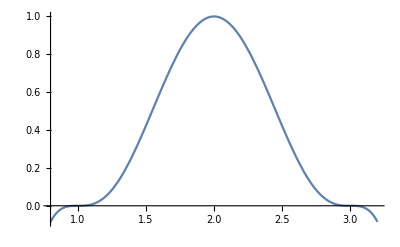

```mathematica
Plot[
Evaluate[(eq13[[2]] /. v1-> 1 /. v2-> 3) ] , {v,0.8,3.2}]
```